```mathematica
Clear["`*"]
(*r vectors here contain the r and θ components. Module converts them to polar for plotting*)
S[R1_,R2_,s1_,s2_]:=Module[{r1,r2,θ1,θ2,rij,rijhat},
r1=R1[[1]];
θ1=R1[[2]];
r2=R2[[1]];
θ2=R2[[2]];
rij={r2*Cos[θ2]-r1*Cos[θ1],r2*Sin[θ2]-r1*Sin[θ1]};
rijhat=rij/√((r2*Cos[θ2]-r1*Cos[θ1])^2+(r2*Sin[θ2]-r1*Sin[θ1])^2);
3*(s1.rijhat)(s2.rijhat)-s1.s2
]
```

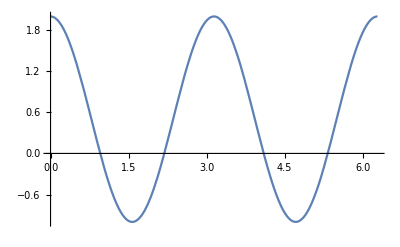

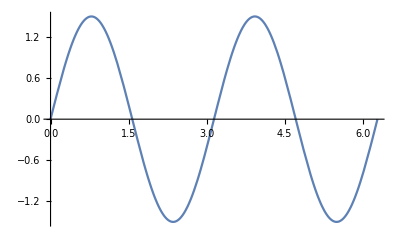

-Graphics-

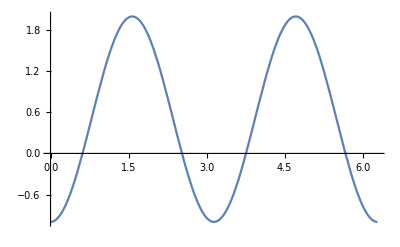

```mathematica
r1={0,0};
r2={1,θ2};
s1={1,0};
s2={1,0};
Plot[S[r1,r2,s1,s2],{θ2,0,2π}]
r1={0,0};
r2={1,θ2};
s1={1,0};
s2={0,1};
Plot[S[r1,r2,s1,s2],{θ2,0,2π}]
r1={0,0};
r2={1,θ2};
s1={0,1};
s2={1,0};
Plot[S[r1,r2,s1,s2],{θ2,0,2π}]
r1={0,0};
r2={1,θ2};
s1={0,1};
s2={0,1};
Plot[S[r1,r2,s1,s2],{θ2,0,2π}]
```